# R0 on a landscape

We want to show how the landscape-level R0 value can affect things like time to extinction, but also look at how a theoretically calculated vs a simulated R0 value compare. 

What this will look like is: 
- Setting up some simulations to look at how changing R0 will change the results. Goal here is to:
	1. Loop over R0 ∈ {0.8,1.0,…,2.6}
	2. For each R0​, compute:
		-extinction time per run
		-mean & variance of infected counts over time
		-max proportion infected
		-epidemic size
		-duration above threshold (e.g. It>10It​>10)
	3. Aggregate summary statistics across 1000 simulations

## R0 changing persistence of pathogen

```mathematica
(* 1. PARAMETERS AND SETUP --------------------------------------------------- *)

ClearAll["Global`*"]
SeedRandom[123]; (* set seed so stuff is reproducible *)
(*First, some directory stuff for outputting plot*)
baseDir="/Users/colebrookson/github/theRmal-landscape/";
figsDir=FileNameJoin[{baseDir,"figs"}];
relativePath[parts__]:=FileNameJoin[{baseDir,parts}];

numPatches = 200000; (* number of spatial patches *)
initialInfected = 1; (* start with just one infected person *)
r0Values = Range[0.8, 2.6, 0.2]; (* range of quasi-r0 values *)
numReps = 100; (* how many runs to average over *)
maxTime = 100; (* max timesteps per run *)
threshold = 100000; (* for tracking how long the outbreak stays "big" *)
weights = ConstantArray[1/numPatches, numPatches]; (* uniform patch weight *)

(* 2. FUNCTION TO RUN ONE SIMULATION ----------------------------------------- *)

simulateRun[totalIndividuals_] := Module[
  {
    t = 0, NI = initialInfected, NT = totalIndividuals,
    infectedHistory = {}, Sloc, Iloc, cloc
  },

  (* while there's still infecteds and we haven't hit time limit *)
  While[NI > 0 && t < maxTime,
  
    (* randomly assign susceptibles and infecteds to patches *)
    Sloc = RandomChoice[weights -> Range[1, numPatches], NT - NI];
    Iloc = RandomChoice[weights -> Range[1, numPatches], NI];

    (* get list of patch IDs that have both S and I *)
    cloc = Intersection[Sloc, Iloc];

    (* count how many susceptibles were in those shared patches = new infecteds *)
    NI = Total[Count[Sloc, #] & /@ cloc];

    (* store current number of infecteds *)
    infectedHistory = Append[infectedHistory, NI];
    t++
  ];

  (* return summary stats for the run *)
  <|
    "ExtinctionTime" -> t,
    "InfectedTimeSeries" -> infectedHistory,
    "MaxProportionInfected" -> Max[infectedHistory]/totalIndividuals,
    "EpidemicSize" -> Total[infectedHistory],
    "DurationAboveThreshold" -> Count[infectedHistory, x_ /; x > threshold]
  |>
]

(* 2.1 FASTER FUNCTION MAYBE ------------------------------------------------- *)
ClearAll[simulateRunSparse]

simulateRunSparse[totalIndividuals_] := Module[
  {
    t = 0,
    IT = initialInfected,         (* current infecteds *)
    NT = totalIndividuals,        (* total population *)
    history = {},                 (* time-series record *)
    occ, patchSample, numInfPatches, sus, p, newInf,
    P = numPatches
  },

  occ = SparseArray[{}, {P}];     (* initialise empty occupancy vector *)

  While[IT > 0 && t < maxTime,

    (* 1 — drop infecteds on patches (sparse update) *)
    patchSample = RandomInteger[{1, P}, IT];
    occ += SparseArray[Normal[Counts[patchSample]], {P}];

    (* 2 — how many patches now have ≥1 infected? *)
    numInfPatches = Length@occ["NonzeroPositions"];

    (* 3 — draw new infections among susceptibles             *)
    sus = NT - IT;                (* susceptibles this step   *)
    p   = N[numInfPatches]/P;     (* share-a-patch probability*)
    newInf = If[sus <= 0,
                0,
                RandomVariate[BinomialDistribution[sus, p]]
              ];

    (* 4 — book-keeping *)
    AppendTo[history, IT];
    IT  = newInf;
    occ = SparseArray[{}, {P}];   (* infecteds die after one step *)
    t++
  ];

  <|
    "ExtinctionTime"         -> t,
    "InfectedTimeSeries"     -> history,
    "MaxProportionInfected"  -> Max[history]/totalIndividuals,
    "EpidemicSize"           -> Total[history],
    "DurationAboveThreshold" -> Count[history, x_ /; x > threshold]
  |>
]
```

### Run the simulations if needed or READ THEM FROM A FILE below this chunk

```mathematica
(* -------------------------------------------------------------- *)
(* 1 — ensure the parallel pool is up; count how many kernels     *)
LaunchKernels[];
numCores = $KernelCount;   (* how many kernels ParallelTable can use *)

(* -------------------------------------------------------------- *)
(* 2 — run the simulation block and time it                       *)
start  = AbsoluteTime[];

simulationResults = Association[];

Do[
  Module[
    {
      Nt = Round[r0*numPatches + initialInfected],
      counter = 0, results, extinctionTimes, timeSeriesList,
      propMax, sizes, durations, aligned, meanOverTime, varOverTime, maxLen
    },
    
    Print["Running simulations for R₀ = ", r0, " (Nt = ", Nt, ") …"];
    SetSharedVariable[counter];
    
    results = Monitor[
      ParallelTable[
        Module[{out = simulateRunSparse[Nt]},
          counter++; out],
        {numReps}
      ],
      Row[{
        "Progress: ", counter, "/", numReps, " (",
        Round[100.0*counter/numReps], "%)"
      }]
    ];
    
    (* ---- unpack and store results ---- *)
    extinctionTimes  = results[[All, "ExtinctionTime"]];
    timeSeriesList   = results[[All, "InfectedTimeSeries"]];
    propMax          = results[[All, "MaxProportionInfected"]];
    sizes            = results[[All, "EpidemicSize"]];
    durations        = results[[All, "DurationAboveThreshold"]];
    
    maxLen  = Min[maxTime, Max[Length /@ timeSeriesList]];
    aligned = Transpose[PadRight[#, maxLen, 0] & /@ timeSeriesList];
    
    meanOverTime = Mean /@ aligned;
    varOverTime  = Variance /@ aligned;
    
    simulationResults[r0] = <|
      "ExtinctionTimes"          -> extinctionTimes,
      "MeanInfectedOverTime"     -> meanOverTime,
      "InfectedTimeSeries"       -> timeSeriesList,
      "VarianceInfectedOverTime" -> varOverTime,
      "MaxProportionInfected"    -> propMax,
      "EpidemicSizes"            -> sizes,
      "DurationsAboveThreshold"  -> durations,
      "ExtinctionProbability"    -> Count[extinctionTimes, t_ /; t < maxTime]/numReps
    |>;
  ],
  {r0, r0Values}
];

elapsed = AbsoluteTime[] - start;   (* seconds *)

(* -------------------------------------------------------------- *)
(* 3 — human-readable summary                                     *)
Print[
  Row[{
    "Finished in ", NumberForm[elapsed, {8, 2}], " s  |  ",
    "numReps = ", numReps, ",  maxTime = ", maxTime, 
    ",  numPatches = ", numPatches, "  |  ",
    "parallel kernels = ", numCores
  }]
];

(* -------------------------------------------------------------- *)
(* 4 — export results                          *)
Export[
  FileNameJoin[{NotebookDirectory[], "..", "..", "outputs", 
                "intermediate-obs", "simResults.wl"}],
  simulationResults
]
```

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

Running simulations for R₀ = 0.8 (Nt = 160001) …

Running simulations for R₀ = 1. (Nt = 200001) …

Running simulations for R₀ = 1.2 (Nt = 240001) …

Running simulations for R₀ = 1.4 (Nt = 280001) …

Running simulations for R₀ = 1.6 (Nt = 320001) …

Running simulations for R₀ = 1.8 (Nt = 360001) …

Running simulations for R₀ = 2. (Nt = 400001) …

Running simulations for R₀ = 2.2 (Nt = 440001) …

Running simulations for R₀ = 2.4 (Nt = 480001) …

Running simulations for R₀ = 2.6 (Nt = 520001) …

Finished in 392.06 s  |  numReps = 100,  maxTime = 100,  numPatches = 200000  |  parallel kernels = 12

/Users/colebrookson/github/theRmal-landscape/src/mathematica/../../outputs/intermediate-obs/simResults.wl

```mathematica
(* read in instead of re-running *)
If[
  !ValueQ[simulationResults], 
  simulationResults = Import[
    FileNameJoin[
      {NotebookDirectory[], "..", "..", "outputs", "intermediate-obs", "simResults.wl"}
    ]
  ]
]
```

#### Let’s get a summary table so we can see roughly what the results say:

```mathematica
CI95[data_] := Quantile[data, {0.025, 0.975}];

summarizeR0[r_] := Module[
  {
    ext = simulationResults[r]["ExtinctionTimes"],
    epi = simulationResults[r]["EpidemicSizes"],
    dur = simulationResults[r]["DurationsAboveThreshold"],
    extCI, epiCI, durCI, varExt, varEpi, varDur
  },
  
  extCI = CI95[ext];
  epiCI = CI95[epi];
  durCI = CI95[dur];
  varExt = Variance[ext];
  varEpi = Variance[epi];
  varDur = Variance[dur];
  
  With[{round = Round[#, 0.01] &},  (* round to 2 decimal places *)
    {
      r,
      round@Mean[ext], round@extCI[[1]], round@extCI[[2]],
      round@Mean[epi], round@epiCI[[1]], round@epiCI[[2]],
      round@Mean[dur], round@durCI[[1]], round@durCI[[2]],
      round@varExt, round@varEpi, round@varDur
    }
  ]
];

summaryData = Prepend[
  summarizeR0 /@ r0Values,
  {
    "R₀",
    "Mean time to I=0", "I=0 CI Low", "I=0 CI High",
    "Mean Size", "CI Low", "CI High",
    "Mean Duration", "CI Low", "CI High", 
    "Var Time", "Var Size", "Var Duration"
  }
];
Grid[
  summaryData,
  Frame -> All,
  Alignment -> Center,
  Background -> {None, {LightGray, {}}},
  ItemStyle -> Directive[FontFamily -> "Helvetica", 12]
]
```

R₀ | Mean time to I=0 | I=0 CI Low | I=0 CI High | Mean Size | CI Low | CI High | Mean Duration | CI Low | CI High | Var Time | Var Size | Var Duration
0.8 | 2.79 | 1. | 12. | 5.9 | 1. | 29. | 0. | 0. | 0. | 10.29 | 334.66 | 0.
1. | 7.98 | 1. | 100. | 122.46 | 1. | 1198. | 0. | 0. | 0. | 324.77 | 487623. | 0.
1.2 | 26.06 | 1. | 100. | 298284. | 1. | 1.42342×10^6 | 0. | 0. | 0. | 1748.91 | 2.94912×10^11 | 0.
1.4 | 47.38 | 1. | 100. | 1.64047×10^6 | 1. | 3.82122×10^6 | 0. | 0. | 0. | 2387.33 | 3.20474×10^12 | 0.
1.6 | 72.48 | 1. | 100. | 4.29289×10^6 | 1. | 6.20574×10^6 | 0. | 0. | 0. | 1967.61 | 7.26058×10^12 | 0.
1.8 | 75.35 | 1. | 100. | 6.25262×10^6 | 1. | 8.57065×10^6 | 57.29 | 0. | 79. | 1841.36 | 1.31865×10^13 | 1107.48
2. | 77.4 | 1. | 100. | 8.21407×10^6 | 1. | 1.0924×10^7 | 62.63 | 0. | 83. | 1727.41 | 2.03801×10^13 | 1184.94
2.2 | 90.1 | 1. | 100. | 1.16723×10^7 | 1. | 1.32266×10^7 | 75.31 | 0. | 85. | 891. | 1.53252×10^13 | 638.16
2.4 | 88.17 | 1. | 100. | 1.34698×10^7 | 1. | 1.5572×10^7 | 75.35 | 0. | 87. | 1036.73 | 2.50237×10^13 | 783.22
2.6 | 87.14 | 1. | 100. | 1.53686×10^7 | 1. | 1.78984×10^7 | 75.81 | 0. | 88. | 1117.96 | 3.56711×10^13 | 868.05

### Plotting the results from the simulations:

#### We want plots that show: 1) the histogram of time to I = 0 for each value of R0

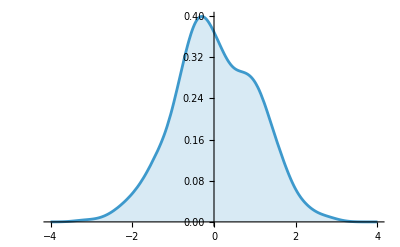

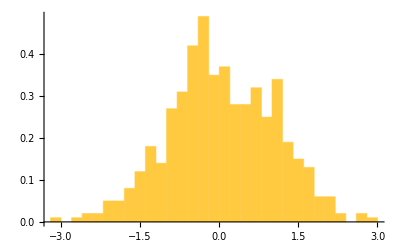

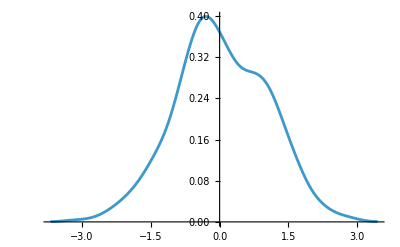

```mathematica
data = RandomVariate[NormalDistribution[0, 1], 500];
dist = SmoothKernelDistribution[data];

Plot[PDF[dist, x], {x, -4, 4}, Filling -> Axis]
Histogram[data, 20, "PDF"]
SmoothHistogram[data]
```

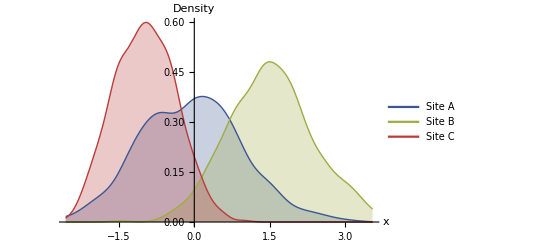

```mathematica
SeedRandom[42];

(* grouped data *)
dataBySite = <|
  "Site A" -> RandomVariate[NormalDistribution[0, 1], 600],
  "Site B" -> RandomVariate[NormalDistribution[1.5, 0.8], 600],
  "Site C" -> RandomVariate[NormalDistribution[-1, 0.6], 600]
|>;

(* build one KDE per site — Map maps over values of an Association *)
dists = Map[SmoothKernelDistribution, dataBySite];
(* optionally: dists = KeyValueMap[#1 -> SmoothKernelDistribution[#2] &, dataBySite]; *)

(* common x-range across groups *)
qMinMax = Map[Quantile[#, {0.005, 0.995}] &, Values[dataBySite]];
{xMin, xMax} = Through[{Min, Max}[qMinMax]];

sites   = Keys[dataBySite];
colors  = ColorData["DarkRainbow"] /@ Rescale[Range[Length@sites]];

n = Length@sites;

Plot[
  Evaluate@Table[PDF[dists[site], x], {site, sites}],
  {x, xMin, xMax},
  PlotRange   -> All,
  PlotStyle   -> (Directive[#, Thick] & /@ colors),
  Filling     -> Axis,  (* or Table[i -> Axis, {i, n}] *)
  FillingStyle ->
    Thread[Range[n] -> (Directive[#, Opacity[.28]] & /@ colors)],
  AxesLabel   -> {"x", "Density"},
  PlotLegends -> Placed[LineLegend[colors, sites, LegendMarkerSize -> 15], After],
  ImagePadding -> 20
]
```

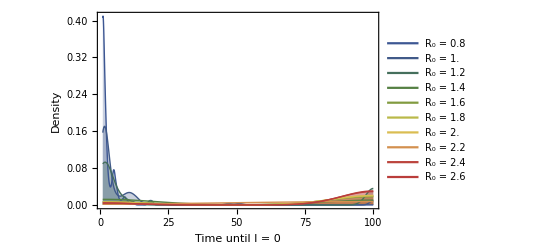

```mathematica
(* === Per-R0 filled KDEs of extinction times ============================== *)
(* 1) order keys and extract data *)
r0s = SortBy[Keys@simulationResults, N];            (* numeric order *)

extPerR0 = (simulationResults /@ r0s)[[All, "ExtinctionTimes"]];
(*          ^^^^^^^^^^^^^^^^^^^^^^^^
   list of sub-associations          use Part [[All, "ExtinctionTimes"]]  *)

dataByR0 = AssociationThread[r0s, extPerR0];

(* optional: drop empty/non-numeric groups *)
dataByR0 = Select[dataByR0, VectorQ[#, NumericQ] && Length[#] > 0 &];

(* 2) one KDE per group; set bandwidth as you like *)
bw    = Automatic;             (* e.g., 0.6 or "Scott" also work *)
dists = Map[SmoothKernelDistribution[#, bw] &, dataByR0];

(* 3) common x-range (robust) *)
qMinMax = Map[Quantile[#, {0.01, 0.99}] &, Values@dataByR0];
{xMin, xMax} = {Max[0, Min@qMinMax[[All, 1]]], Max@qMinMax[[All, 2]]};

(* 4) colors/labels *)
n      = Length@dataByR0;
keys   = Keys@dataByR0; (* same order as r0s *)
colors = ColorData["DarkRainbow"] /@ Rescale[Range@n];
labels = Row[{"R₀ = ", #}] & /@ keys;

(* 5) plot per-curve filled KDEs with matching fills *)
Plot[
  Evaluate@Table[PDF[dists[r0], x], {r0, keys}],
  {x, xMin, xMax},
  Frame       -> True,
  FrameLabel  -> {"Time until I = 0", "Density"},
  PlotRange   -> All,
  PlotStyle   -> (Directive[#, Thick] & /@ colors),
  Filling     -> Axis,
  FillingStyle ->
    Thread[Range@n -> (Directive[#, Opacity[.28]] & /@ colors)],
  PlotLegends -> Placed[LineLegend[colors, labels, LegendMarkerSize -> 15], After],
  ImagePadding -> 20
]
```

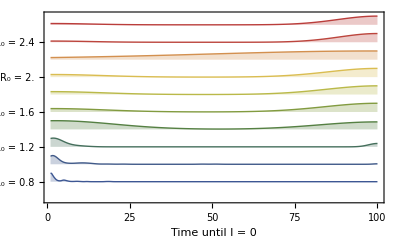

figDir

Export::chtype: First argument FileNameJoin[{figDir,extinction-time-vs-r0-ridge.pdf}] is not a valid file specification.

```mathematica
(* === Ridge plot of extinction-time densities by R₀ ======================= *)
(* expects: simulationResults ::
   <| 0.8 -> <|"ExtinctionTimes" -> {...}, ...|>, 1.0 -> <|...|>, ... |> *)

(* 1) pull data per R0 *)
r0s = SortBy[Keys@simulationResults, N];
extPerR0 = (simulationResults /@ r0s)[[All, "ExtinctionTimes"]];
dataByR0 = AssociationThread[r0s, extPerR0];
dataByR0 = Select[dataByR0, VectorQ[#, NumericQ] && Length[#] > 0 &];

(* 2) KDEs *)
bw    = Automatic; 
dists = Map[SmoothKernelDistribution[#, bw] &, dataByR0];

(* 3) common x-range + evaluation grid *)
qMinMax = Map[Quantile[#, {0.01, 0.99}] &, Values@dataByR0];
{xMin, xMax} = {Max[0, Min@qMinMax[[All, 1]]], Max@qMinMax[[All, 2]]};
xGrid = Subdivide[xMin, xMax, 300];

(* 4) colors and ridge spacing *)
keys   = Keys@dataByR0;
n      = Length@keys;
colors = ColorData["DarkRainbow"] /@ Rescale[Range@n];
offset = 2;  (* vertical spacing between ridges *)

(* 5) build filled polygons, each normalized to peak=1 for visual clarity *)
ridgePolys =
  MapThread[
    Function[{r0, col},
      Module[{y = PDF[dists[r0], xGrid], yScale, yOff, poly, line},
        yScale = If[Max@y > 0, y/Max@y, y];
        yOff   = offset*(First@First@Position[keys, r0] - 1);
        poly   = Polygon@Join[Transpose[{xGrid, yScale}], {{Last@xGrid, 0}, {First@xGrid, 0}}];
        line   = Line@Transpose[{xGrid, yScale}];

        {
          (* filled area with scoped style *)
          Style[Translate[poly, {0, yOff}], 
            {FaceForm[Directive[col, Opacity[.28]]], EdgeForm[None]}],
          (* outline with scoped style *)
          Style[Translate[line, {0, yOff}], Directive[col, Thick]]
        }
      ]
    ],
    {keys, colors}
  ] // Flatten;

(* 6) y-axis ticks: one label per R0 at each ridge's baseline *)
yTicks =
  Table[{offset*(i - 1), Row[{"R₀ = ", keys[[i]]}]}, {i, n}];

plot = Graphics[
  ridgePolys,
  Frame -> True,
  FrameLabel -> {"Time until I = 0", None, None, None},
  FrameTicks -> {{yTicks, None}, {Automatic, None}},
  PlotRange -> {{xMin, xMax}, {-offset, offset*(n - 1) + 1.05}},
  ImagePadding -> {{50, 10}, {40, 10}},  (* add a bit more bottom space *)
  AspectRatio -> 0.6
];
Print[plot];
Export[FileNameJoin[{figDir, "extinction-time-vs-r0-ridge.pdf"}],  plot,  "PDF"];
```

#### 2) the mean extinction time per R0

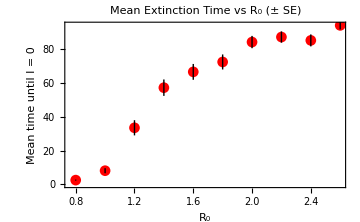

```mathematica
(* 5. MEAN EXTINCTION TIME VS R₀ (with error bars drawn manually) ------------ *)
figDir = FileNameJoin[{NotebookDirectory[], "..", "..", "figs", "si", "r0-simulations"}];
If[! DirectoryQ[figDir], CreateDirectory[figDir, CreateIntermediateDirectories -> True]];

Module[
  {rVals, means, sds, ses, basePoints, errorBars, plot, numReps},

  rVals = r0Values;
  numReps = 100; (* adjust to whatever was used during simulations *)

  (* compute mean and SD of extinction times per R₀ *)
  means = Mean /@ (simulationResults[#]["ExtinctionTimes"] & /@ rVals);
  sds = StandardDeviation /@ (simulationResults[#]["ExtinctionTimes"] & /@ rVals);

  (* compute standard error = SD / sqrt(n) *)
  ses = sds / Sqrt[numReps];

  basePoints = Transpose[{rVals, means}];

  (* draw vertical error bars for ±SE *)
  errorBars = Table[
    {
      Black,
      Line[{{rVals[[i]], means[[i]] - ses[[i]]}, {rVals[[i]], means[[i]] + ses[[i]]}}]
    },
    {i, Length[rVals]}
  ];

  plot = Show[
    ListPlot[
      basePoints,
      PlotStyle -> Red,
      PlotMarkers -> Automatic,
      Frame -> True,
      FrameLabel -> {"R₀", "Mean time until I = 0"},
      PlotLabel -> "Mean Extinction Time vs R₀ (± SE)",
      ImageSize -> Medium
    ],
    Graphics[errorBars]
  ];

  Print[plot];
  Export[FileNameJoin[{figDir, "extinction-time-vs-r0.png"}],  plot,  "PNG"]; 
]
```

## Look at how many sims out of n go to I=0 at t=1.

### In theory this will tell us how “fragile” the system is out of the gate

<|0.8→0,1.→0,1.2→0,1.4→0,1.6→0,1.8→0,2.→0,2.2→0,2.4→0,2.6→0|>

{{1,3,2},{1},{1,1,1,1},{1,1,1},{1,1},{1,1,2,2,4,3,3,2,3,4,1,1,1,1,1},{1,2,1,1},{1},{1},{1},{1,1,1},{1},{1},{1},{1,1},{1,2,1,1},{1},{1,1},{1},{1,1,1},{1},{1},{1,2,2,2,2,2},{1},{1},{1,1,1},{1},{1},{1},{1,1},{1,1},{1},{1},{1,1,1},{1},{1},{1,2,3,1,4,3},{1},{1,1},{1},{1},{1},{1,1,1,2},{1,1,3},{1,1,1},{1},{1,1,1},{1,2,3,3,2,2,2,2,1},{1},{1,3,2,2,1,2},{1},{1},{1,1},{1},{1,1,2,2,3,1,1,2,3,1},{1,1,1,2},{1,1,1},{1,1,1,3,3,1,1,2,4,3,3,1,3,2,5,5,3,5,3,1},{1,1,1,1},{1},{1},{1,1},{1,2,1,2},{1,2,1,4},{1},{1,2},{1},{1},{1},{1,1,1,1,2,2},{1},{1},{1},{1,1},{1,2},{1,1},{1,1},{1,2,3,3,2,3,2,1},{1},{1,1,1,2,1,2,2},{1},{1,1},{1},{1},{1},{1},{1},{1,1},{1},{1},{1},{1,1},{1},{1,2,2,3,4,5,3},{1},{1},{1},{1,1},{1},{1,1,2,2,1}}

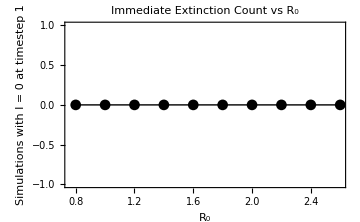

```mathematica
(* 7. COUNT EXTINCTION AT FIRST STEP (t = 1) FOR EACH R₀ -------------------- *)

earlyExtinctionCounts = Association[];

Do[
  Module[{timeSeriesList, extinctNow},
    
    timeSeriesList = simulationResults[r0]["InfectedTimeSeries"];
    (* count how many have I=0 at timestep 1 *)
    extinctNow = Count[timeSeriesList, ts_ /; Length[ts] >= 2 && ts[[2]] == 0];
    earlyExtinctionCounts[r0] = extinctNow;
  ],
  {r0, r0Values}
];

(* view the result *)
earlyExtinctionCounts
simulationResults[0.8]["InfectedTimeSeries"]
(* 8. FIXED VERSION: SORTED R₀ VALUES ON X-AXIS ----------------------------- *)

Module[{rVals, counts, points, plot},

  (* extract and sort keys *)
  rVals = Sort[Keys[earlyExtinctionCounts]];
  counts = Lookup[earlyExtinctionCounts, rVals];

  points = Transpose[{rVals, counts}];

  plot = ListLinePlot[
    points,
    PlotStyle -> {Thick, Black},
    PlotMarkers -> Automatic,
    Frame -> True,
    FrameLabel -> {"R₀", "Simulations with I = 0 at timestep 1"},
    PlotLabel -> "Immediate Extinction Count vs R₀",
    ImageSize -> Medium
  ];

  Print[plot];
]
```

### Let’s try this for # of sims where I=0 at t=5

<|0.8→0,1.→0,1.2→0,1.4→0,1.6→0,1.8→0,2.→0,2.2→0,2.4→0,2.6→0|>

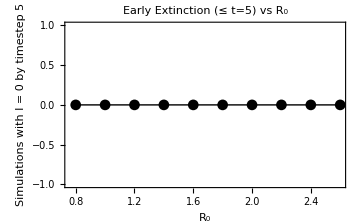

```mathematica
(* 9. COUNT EXTINCTIONS BY TIME t = 5 FOR EACH R₀ --------------------------- *)

earlyExtinctionBy5 = Association[];

Do[
  Module[{timeSeriesList, extinctBy5},

    timeSeriesList = simulationResults[r0]["InfectedTimeSeries"];

    (* count if any timestep from 1 to 5 hits zero *)
    extinctBy5 = Count[
      timeSeriesList,
      ts_ /; AnyTrue[Take[ts, UpTo[100]][[2 ;;]], (# == 0 &)]
    ];

    earlyExtinctionBy5[r0] = extinctBy5;
  ],
  {r0, r0Values}
];
earlyExtinctionBy5
(* 10. PLOT: EXTINCTION BY t = 5 VS R₀ -------------------------------------- *)

Module[{rVals, counts, points, plot},

  rVals = Sort[Keys[earlyExtinctionBy5]];
  counts = Lookup[earlyExtinctionBy5, rVals];
  points = Transpose[{rVals, counts}];

  plot = ListLinePlot[
    points,
    PlotStyle -> {Thick, Black},
    PlotMarkers -> Automatic,
    Frame -> True,
    FrameLabel -> {"R₀", "Simulations with I = 0 by timestep 5"},
    PlotLabel -> "Early Extinction (≤ t=5) vs R₀",
    ImageSize -> Medium
  ];

  Print[plot];
]
```

## Moving to weights given by an actual distribution

### We want to look what happens if we allow the weights to come from a uniform distribution something like then as q goes away from 0 towards 1/n then that means an increase in heterogeneity then in theory this increases the R0 on the landscape.

```mathematica
(* ::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::: *)
(*  FAST q-sweep:  R₀ increases as weight heterogeneity (q) grows                    *)
(*  – no per-individual sampling                                                    *)
(*  – no Intersection[Sloc,Iloc]                                                   *)
(*  – all stats identical to your original Association structure                   *)
(* ::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::: *)

SeedRandom[42];

(* ---------------- core parameters (same symbols as before) ---------------- *)
r0              = 1.8;
numPatches      = 2000000;
initialInfected = 1;

S  = r0*numPatches;        (* 10000.  – machine real *)
SInt = Round[S];           (* 10000   – exact integer *)

Nt = SInt + initialInfected;

numReps   = 100000;                (*   ‼ make this big only after profiling *)
qValues   = Range[0, 1/numPatches, 1/(5*numPatches)];

(* helper: draw “raw” weights once, normalise to sum 1 ----------------------- *)
generatePatchWeights[q_] := Module[{raw},
  raw = RandomReal[{1/numPatches - q, 1/numPatches + q}, numPatches];
  raw/Total[raw]
];

(* ===== 1. landscape-fixed, many replicates on the same weights ============= *)
simulateR0FastSameWeights[q_, reps_] := Module[
  {weights, pickIdx, wSelected},
  
  weights   = generatePatchWeights[q];
  (* draw indices of infected patches reps×, weighted by patch probabilities *)
  pickIdx   = RandomChoice[weights -> Range[numPatches], reps];
  wSelected = weights[[pickIdx]];              (* vector of chosen weights   *)
  
  (* vectorised Binomial draws: new infections for each replicate            *)
  RandomVariate[BinomialDistribution[SInt, #]] & /@ wSelected
];

(* ===== 2. “fresh-weights each replicate” but only one Binomial per run ===== *)
simulateR0FastFreshWeights[q_] := Module[
  {raw, total, infectedWeight},
  
  (* generate weights just far enough to get the infected patch’s weight *)
  raw           = RandomReal[{1/numPatches - q, 1/numPatches + q}, numPatches];
  total         = Total[raw];
  infectedWeight = RandomChoice[raw -> (raw/total)];  (* pick weight itself *)
  
  RandomVariate[BinomialDistribution[SInt, infectedWeight]]
];

(* choose which driver we want ------------- *)
ClearAll[simulateR0Sample]
(*simulateR0Sample[q_, reps_] := simulateR0FastSameWeights[q, reps];     (* << preferred *)*)
 simulateR0Sample[q_, reps_] := Table[simulateR0FastFreshWeights[q], {reps}]; 

(* --------------------- MAIN q-sweep, timed --------------------------------- *)
LaunchKernels[];
numCores  = $KernelCount;

Print["Running q-sweep on ", numCores, " kernels …"];
t0 = AbsoluteTime[];

r0ComparisonResults = Association[];

Do[
  Module[{simVals, simMean, theoryR0},
    Print["  q = ", NumberForm[q, {3, 5}], " …"];
    
    simVals = simulateR0FastSameWeights[q, numReps];
    simVals  = Flatten[simVals];            (* gather results from kernels  *)
    
    simMean  = Mean[simVals];
    theoryR0 = (S/numPatches) + numPatches*S*(q^2/3.);
    
    r0ComparisonResults[q] = <|
      "SimulatedR0"        -> simMean,
      "TheoreticalR0"      -> theoryR0,
      "FirstStepInfections"-> simVals
    |>;
  ],
  {q, qValues}
];

dt = AbsoluteTime[] - t0;
Print[
  "Finished in ", NumberForm[dt, {7, 1}], " s  |  ", 
  "numReps = ", numReps, ",  numPatches = ", numPatches, 
  ",  parallel kernels = ", numCores
];

Export[
  FileNameJoin[{NotebookDirectory[], "..", "..", "outputs",
                "intermediate-obs", "qVarSimResults_fast.wl"}],
  r0ComparisonResults
]
```

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

Running q-sweep on 12 kernels …

q = 0 …

q = 1/10000000 …

q = 1/5000000 …

q = 3/10000000 …

q = 1/2500000 …

q = 1/2000000 …

Finished in 9.1 s  |  numReps = 100000,  numPatches = 2000000,  parallel kernels = 12

/Users/colebrookson/github/theRmal-landscape/src/mathematica/../../outputs/intermediate-obs/qVarSimResults_fast.wl

```mathematica
(* read in instead of re-running *)
If[
  !ValueQ[r0ComparisonResults], 
  r0ComparisonResults = Import[
    FileNameJoin[
      {NotebookDirectory[], "..", "..", "outputs", "intermediate-obs", "qVarSimResults.wl"}
    ]
  ]
]
```

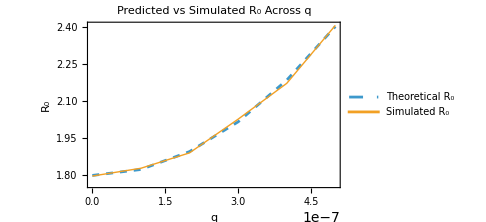

```mathematica
(* 11. PLOT: THEORETICAL VS SIMULATED R₀ (FIXED) ---------------------------- *)

Module[
  {qs, simVals, theoryVals, plot},

  (* 1. get the sorted q-values *)
  qs = Sort[Keys[r0ComparisonResults]];

  (* 2. extract the numeric fields from each inner assoc *)
  simVals = (r0ComparisonResults[#]["SimulatedR0"] &) /@ qs;
  theoryVals = (r0ComparisonResults[#]["TheoreticalR0"] &) /@ qs;

  (* 3. build the two curves: first theoretical, then simulated *)
  plot = ListLinePlot[
    {
      Transpose[{qs, theoryVals}],
      Transpose[{qs, simVals}]
    },
    PlotStyle -> {
      {Dashed},                    (* theoretical: dashed line *)
      {Thick, Automatic}           (* simulated: thick line + markers *)
    },
    PlotMarkers -> {None, Automatic},
    PlotLegends -> {"Theoretical R₀", "Simulated R₀"},
    Frame -> True,
    FrameLabel -> {"q", "R₀"},
    PlotLabel -> "Predicted vs Simulated R₀ Across q",
    ImageSize -> Medium
  ];

  Print[plot];
  Export[FileNameJoin[{figDir, "predicted-vs-simulated-r0-with-q.png"}],  plot,  "PNG"]; 
]
```

```mathematica
r0ComparisonResults;
```

```mathematica
qs = Keys[r0ComparisonResults];  (* use actual keys *)

simVals = Association[
  Table[q -> r0ComparisonResults[q]["SimulatedR0"], {q, qs}]
];

seVals = Association[
  Table[
    q -> StandardDeviation[r0ComparisonResults[q]["FirstStepInfections"]] / 
           Sqrt[Length[r0ComparisonResults[q]["FirstStepInfections"]]],
    {q, qs}
  ]
]
```

<|0→(√(1438091/55555))/1200,1/10000000→(√(62275493/33333))/10000,1/5000000→(√(5100914791/11111))/150000,3/10000000→(√(5902657079/11111))/150000,1/2500000→(√(423155929/11111))/37500,1/2000000→(√(7810882879/11111))/150000|>

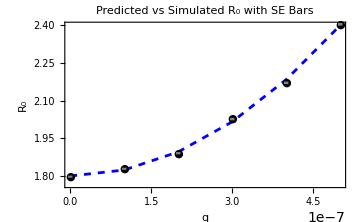

```mathematica
Module[
  {points, errorBars, meanList, seList, theoryVals, theoryLine},

  (* prepare mean and SE values *)
  points = Transpose[{qs, Values[simVals]}];
  meanList = Values[simVals];
  seList = Values[seVals];

  (* generate error bars manually using SE *)
  errorBars = Table[
    {
      Thickness[0.009],
      Gray,
      Line[{
        {qs[[i]], meanList[[i]] - seList[[i]]},
        {qs[[i]], meanList[[i]] + seList[[i]]}
      }]
    },
    {i, Length[qs]}
  ];

  (* compute theoretical R₀ values *)
  theoryVals = (S/numPatches + numPatches*S*(#^2/3) &) /@ qs;
  theoryLine = Transpose[{qs, theoryVals}];

  (* plot objects *)
  theoryPlot = ListLinePlot[
    theoryLine,
    PlotStyle -> {Dashed, Blue}
  ];

  simPlot = ListPlot[
    points,
    PlotStyle -> Black,
    PlotMarkers -> "●"
  ];

  (* final combined plot *)
  plotPointV = Show[
    theoryPlot,
    simPlot,
    Graphics[errorBars],
    Frame -> True,
    FrameLabel -> {"q", "R₀"},
    PlotLabel -> "Predicted vs Simulated R₀ with SE Bars",
    PlotLegends -> LineLegend[
      {"Theoretical R₀", "Simulated R₀ ± SE"},
      LegendMarkerSize -> 20
    ],
    ImageSize -> Medium
  ];
  Export[FileNameJoin[{figDir, "predicted-vs-simulated-r0-with-q-points.png"}],  plotPointV,  "PNG"]; 
  plotPointV
]
```

```mathematica
(* :::::::::::::::::::::::::::::::::::  FAST UNIQUE-PATCH VERSION  ::::::::::::::::::::::::::::::::::: *)
(* 
   assumptions in this stripped-down simulator
   -------------------------------------------------------------
   1. patches are chosen independently with replacement and all
      have equal probability (uniform weights).
   2. an infected individual survives exactly one step, so it
      never matters *which* patch holds how many infecteds –
      only how many *distinct* patches are occupied in a step. 
   3. susceptibles become infected if they land in any currently
      occupied patch; probability = (# infected patches) / P.
   4. we do *not* keep a record of which patch ids were used,
      only the count of unique ids each step.  this sacrifices
      any later spatial analysis that needs explicit ids, but
      buys a huge speed-up (no sparse arrays, no million-cell
      lists, no heavy bookkeeping).
   5. all downstream summaries (extinction time, epidemic size,
      etc.) are identical in format to  original code so the
      rest of pipeline works unchanged.
*)

(* 1.  fast per-run simulator using only unique-patch counts *)
ClearAll[simulateRunUnique]
maxTimeUnique = 1000;
numRepsUnique = 1000;

simulateRunUnique[totalIndividuals_] := Module[
  {t = 0, IT = initialInfected, NT = totalIndividuals,
   history = {},                     (* record infecteds through time *)
   patchSample, numInfPatches, sus, p, newInf, P = numPatches},
  
  While[IT > 0 && t < maxTimeUnique,
    
    (* drop current infecteds onto patches *)
    patchSample   = RandomInteger[{1, P}, IT];
    numInfPatches = Length@DeleteDuplicates[patchSample];
    
    (* draw new infections among susceptibles *)
    sus   = NT - IT;
    p     = N[numInfPatches]/P;      (* share-a-patch probability *)
    newInf = If[sus <= 0, 0,
                RandomVariate[BinomialDistribution[sus, p]]];
    
    AppendTo[history, IT];
    IT = newInf;
    t++
  ];
  
  <|
    "ExtinctionTime"         -> t,
    "InfectedTimeSeries"     -> history,
    "MaxProportionInfected"  -> Max[history]/totalIndividuals,
    "EpidemicSize"           -> Total[history],
    "DurationAboveThreshold" -> Count[history, x_ /; x > threshold]
  |>
]

(*
  ok so we don't actually care which exact patches get hit, only
  whether a susceptible ends up sharing any patch with an infect-ed.

  reasoning:
    • there are p = numPatches identical sites, each chosen with prob 1/p
    • each infected “tags” its own patch ⇒ prob a given patch stays clean
      after it picks is (1-1/p)
    • with it infecteds the chance a *specific* patch is still clean is
          (1-1/p)^it
    • flip viewpoint: for one susceptible the chance it lands on at
      least one tagged patch is
          p_t = 1 - (1-1/p)^it
    • when p is big this is ≈ 1  exp(-it/p)  (handy if you want a float)

  bottom line: we can skip drawing millions of patch labels; just draw
  new infections ~ Binomial[nt-it,  p_t].
*)
ClearAll[simulateRunFast]
simulateRunFast[totalIndividuals_, horizon_: maxTimeUnique] :=
 Module[{t = 0, IT = initialInfected, NT = totalIndividuals,
         history = {}, P = numPatches, p, newInf},
  
  While[IT > 0 && t < horizon,
    p      = 1. - (1. - 1./P)^IT;              (* O(1) *)
    newInf = RandomVariate[BinomialDistribution[NT - IT, p]];
    AppendTo[history, IT];
    IT = newInf; t++];
  
  <|
    "ExtinctionTime"         -> t,
    "InfectedTimeSeries"     -> history,
    "MaxProportionInfected"  -> Max[history]/totalIndividuals,
    "EpidemicSize"           -> Total[history],
    "DurationAboveThreshold" -> Count[history, x_ /; x > threshold]
  |>
]

(* 2.  main simulation loop — identical structure, just swaps in the new function *)
uniqueSimulationResults = Association[];

Do[
  Module[
    {Nt = Round[r0*numPatches + initialInfected],
     counter = 0, results, extinctionTimes, timeSeriesList,
     propMax, sizes, durations, maxLen, aligned, meanOverTime, varOverTime},
    
    Print["Running UNIQUE-PATCH sims for R₀ = ", r0, " (Nt = ", Nt, ")…"];
    SetSharedVariable[counter];
    
    results = Monitor[
      ParallelTable[
        Module[{out = simulateRunFast[Nt]},
          counter++; out],
        {numRepsUnique}
      ],
      Row[{
        "Progress: ", counter, "/", numRepsUnique, " (",
        Round[100.0*counter/numRepsUnique], "%)"
      }]
    ];
    
    extinctionTimes = results[[All, "ExtinctionTime"]];
    timeSeriesList  = results[[All, "InfectedTimeSeries"]];
    propMax         = results[[All, "MaxProportionInfected"]];
    sizes           = results[[All, "EpidemicSize"]];
    durations       = results[[All, "DurationAboveThreshold"]];
    
    maxLen   = Min[maxTimeUnique, Max[Length /@ timeSeriesList]];
    aligned  = Transpose[PadRight[#, maxLen, 0] & /@ timeSeriesList];
    meanOverTime = Mean /@ aligned;
    varOverTime  = Variance /@ aligned;
    
    uniqueSimulationResults[r0] = <|
      "ExtinctionTimes"           -> extinctionTimes,
      "MeanInfectedOverTime"      -> meanOverTime,
      "InfectedTimeSeries"        -> timeSeriesList,
      "VarianceInfectedOverTime"  -> varOverTime,
      "MaxProportionInfected"     -> propMax,
      "EpidemicSizes"             -> sizes,
      "DurationsAboveThreshold"   -> durations,
      "ExtinctionProbability"     -> Count[extinctionTimes, t_ /; t < maxTimeUnique]/numRepsUnique
    |>;
  ],
  {r0, r0Values}
];

(* 3.  export results to the same outputs folder with a distinct filename *)
Export[
  FileNameJoin[
    {NotebookDirectory[], "..", "..", "outputs", "intermediate-obs", "simResults_unique.wl"}
  ],
  uniqueSimulationResults
]

(* 5. MEAN EXTINCTION TIME VS R₀ (with error bars drawn manually) ------------ *)

Module[
  {rVals, means, sds, ses, basePoints, errorBars, plot, numReps},

  rVals = r0Values;
  numReps = numRepsUnique; (* adjust to whatever was used during simulations *)

  (* compute mean and SD of extinction times per R₀ *)
  means = Mean /@ (uniqueSimulationResults[#]["ExtinctionTimes"] & /@ rVals);
  sds = StandardDeviation /@ (uniqueSimulationResults[#]["ExtinctionTimes"] & /@ rVals);

  (* compute standard error = SD / sqrt(n) *)
  ses = sds / Sqrt[numReps];

  basePoints = Transpose[{rVals, means}];

  (* draw vertical error bars for ±SE *)
  errorBars = Table[
    {
      Black,
      Line[{{rVals[[i]], means[[i]] - ses[[i]]}, {rVals[[i]], means[[i]] + ses[[i]]}}]
    },
    {i, Length[rVals]}
  ];

  plot = Show[
    ListPlot[
      basePoints,
      PlotStyle -> Red,
      PlotMarkers -> Automatic,
      Frame -> True,
      FrameLabel -> {"R₀", "Mean time until I = 0"},
      PlotLabel -> "Mean Extinction Time vs R₀ (± SE)",
      ImageSize -> Medium
    ],
    Graphics[errorBars]
  ];

  Print[plot];
]
```

# This section is code I don’t really want for now

I want to see how changing our different components of our expression would change the expected R0

#### 3) A timeseries showing I vs S through time (mostly a sanity check / curiosity)

```mathematica
plotInfectedSusceptibleTimeSeries[r0_] := Module[
  {
    Nt, infectedSeriesList, maxLen, alignedI,
    meanI, stdI, meanS, stdS, timeVec,
    infectedRibbon, susceptibleRibbon, lines, plot
  },

  (* figure out total population *)
  Nt = Round[r0 * numPatches + initialInfected];

  (* get raw time series *)
  infectedSeriesList = simulationResults[r0]["InfectedTimeSeries"];
  maxLen = Max[Length /@ infectedSeriesList];

  (* align all series to same length *)
  alignedI = PadRight[#, maxLen, 0] & /@ infectedSeriesList;

  (* mean and std dev over time *)
  meanI = Mean /@ Transpose[alignedI];
  stdI = StandardDeviation /@ Transpose[alignedI];

  (* susceptible = total - infected, same variance *)
  meanS = Nt - meanI;
  stdS = stdI;

  timeVec = Range[0, maxLen - 1];

  (* draw ribbons *)
  infectedRibbon = {
    LightRed,
    Polygon[
      Join[
        Transpose[{timeVec, meanI - stdI}],
        Reverse[Transpose[{timeVec, meanI + stdI}]]
      ]
    ]
  };

  susceptibleRibbon = {
    LightBlue,
    Polygon[
      Join[
        Transpose[{timeVec, meanS - stdS}],
        Reverse[Transpose[{timeVec, meanS + stdS}]]
      ]
    ]
  };

  (* draw mean curves *)
  lines = {
    Red, Thick, Line[Transpose[{timeVec, meanI}]],
    Blue, Thick, Line[Transpose[{timeVec, meanS}]]
  };

  (* combine everything and return plot *)
  Show[
    Graphics[{infectedRibbon, susceptibleRibbon, lines}],
    Frame -> True,
    FrameLabel -> {"Time", "Number of Individuals"},
    PlotLabel -> Row[{"I and S over time (R₀ = ", r0, ")"}],
    ImageSize -> Medium
  ]
]
plotInfectedSusceptibleTimeSeries[1.0]
plotInfectedSusceptibleTimeSeries[1.6]
plotInfectedSusceptibleTimeSeries[2.4]
```

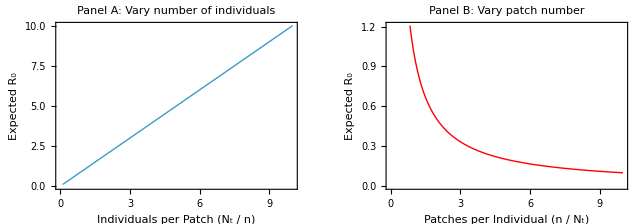
```mathematica
(* RESET AND DEFINE *)
ClearAll[initialInfected, ntRange, nRange, r0Formula, r0DensityData1, r0DensityData2]
initialInfected = 1;

(* Define fixed quantities *)
fixedN = 1000;
fixedNt = 1000;

(* FULL EXPRESSION *)
r0Formula[nt_, n_] := n * (1/n)^2 * (nt - initialInfected)  (* Equivalent to (nt - 1)/n *)

(* PANEL A: Vary Nt, fix n — plot vs. individuals per patch *)
ntRange = Range[100, 10000, 50];
r0DensityData1 = Table[
  {nt/fixedN, r0Formula[nt, fixedN]},   (* x = density *)
  {nt, ntRange}
];

(* PANEL B: Vary n, fix Nt — plot vs. patches per individual *)
nRange = Range[100, 10000, 50];
r0DensityData2 = Table[
  {n/fixedNt, r0Formula[fixedNt, n]},   (* x = inverse density *)
  {n, nRange}
];

(* PANEL A PLOT *)
panelA = ListLinePlot[
  r0DensityData1,
  Frame -> True,
  FrameLabel -> {
    Style["Individuals per Patch (Nₜ / n)", 14],
    Style["Expected R₀", 14]
  },
  PlotLabel -> 
    Style["Panel A: Vary number of individuals", 14, Bold],
  PlotStyle -> Thick,
  ImageSize -> 400
];

(* PANEL B PLOT *)
panelB = ListLinePlot[
  r0DensityData2,
  Frame -> True,
  FrameLabel -> {
    Style["Patches per Individual (n / Nₜ)", 14],
    Style["Expected R₀", 14]
  },
  PlotLabel -> 
    Style["Panel B: Vary patch number", 14, Bold],
  PlotStyle -> {Thick, Red},
  ImageSize -> 400
];

(* COMBINE PLOTS *)
GraphicsRow[{panelA, panelB}, Spacings -> 20]



-Graphics-
```

-Graphics-

-Graphics-

#### First I’ll make a function that generates the weights in a variable way in case I want to change it later:

```mathematica
generateWeights[type_, numPatches_, q_: 0] := Module[{w},
  Switch[type,

    (* equal chance for every patch, nothing fancy *)
    "constant", ConstantArray[1/numPatches, numPatches],

    (* uniform probs, centered at 1/n but wiggly by q *)
    "uniform", Normalize[
      RandomVariate[
        UniformDistribution[{1/numPatches - q, 1/numPatches + q}], 
        numPatches
      ]
    ],

    (* exponential weights, avg is still 1/n *)
    "exponential", Normalize[
      RandomVariate[ExponentialDistribution[numPatches], numPatches]
    ]
  ]
];
```

#### Goal here is to: 1. Loop over R0 ∈ {0.8,1.0,…,2.6} 2. For each R0R0​, compute: extinction time per run mean & variance of infected counts over time max proportion infected epidemic size duration above threshold (e.g. It>10It​>10) 3. Aggregate summary statistics across 1000 simulations

```mathematica
(* PARAMETERS *)
ClearAll["Global`*"]
SeedRandom[123];

numPatches = 1000;
initialInfected = 1;
r0Values = Range[0.8, 2.6, 0.2];
numReps = 1000;
maxTime = 1000;
threshold = 100; (*This is a threshold counter to see for how long each sim stays above this number of indI*)
weights = ConstantArray[1/numPatches, numPatches];

(* FUNCTION TO RUN A SINGLE SIMULATION *)
simulateRun[totalIndividuals_] := Module[
  {t = 0, NI = initialInfected, NT = totalIndividuals, infectedHistory = {}, Sloc, Iloc, cloc, infectedEver = <||>},

  While[NI > 0 && t < maxTime,
    Sloc = RandomChoice[weights -> Range[1, numPatches], NT - NI];
    Iloc = RandomChoice[weights -> Range[1, numPatches], NI];
    cloc = Intersection[Sloc, Iloc];

    NI = Total[Count[Sloc, #] & /@ cloc];
    infectedHistory = Append[infectedHistory, NI];
    t++
  ];

  <|
    "ExtinctionTime" -> t,
    "InfectedTimeSeries" -> infectedHistory,
    "MaxProportionInfected" -> Max[infectedHistory]/totalIndividuals,
    "EpidemicSize" -> Total[infectedHistory],
    "DurationAboveThreshold" -> Count[infectedHistory, x_ /; x > threshold]
  |>
]

(* MAIN LOOP OVER R0 VALUES *)
simulationResults = Association[];

Do[
  Module[{Nt, counter = 0, progress, results, extinctionTimes, timeSeriesList, 
  propMax, sizes, durations, aligned, meanOverTime, varOverTime},
    Nt = Round[r0 * numPatches + initialInfected];
    Print["Running simulations for R₀ = ", r0, " (Nt = ", Nt, ")..."];
    (* Shared progress counter *)
    SetSharedVariable[counter];
    results = Monitor[
      ParallelTable[
        Module[{out = simulateRun[Nt]},
          counter++;
          out
        ],
        {numReps}
      ],
      Row[{
        "Progress: ", counter, "/", numReps, " (", 
        Round[100.0*counter/numReps], "%)"
      }]
    ];

    (* Extract summary data *)
    extinctionTimes = results[[All, "ExtinctionTime"]];
    timeSeriesList = results[[All, "InfectedTimeSeries"]];
    propMax = results[[All, "MaxProportionInfected"]];
    sizes = results[[All, "EpidemicSize"]];
    durations = results[[All, "DurationAboveThreshold"]];

    (* Align time series and compute mean/variance *)
    maxLen = Min[maxTime, Max[Length /@ timeSeriesList]];
    aligned = Transpose[PadRight[#, maxLen, 0] & /@ timeSeriesList];
    meanOverTime = Mean /@ aligned;
    varOverTime = Variance /@ aligned;

    simulationResults[r0] = <|
      "ExtinctionTimes" -> extinctionTimes,
      "MeanInfectedOverTime" -> meanOverTime,
      "VarianceInfectedOverTime" -> varOverTime,
      "MaxProportionInfected" -> propMax,
      "EpidemicSizes" -> sizes,
      "DurationsAboveThreshold" -> durations,
      "ExtinctionProbability" -> Count[extinctionTimes, t_ /; t < maxTime]/numReps
    |>;
  ],
  {r0, r0Values}
];
```

Running simulations for R₀ = 0.8 (Nt = 801)...

Running simulations for R₀ = 1. (Nt = 1001)...

```mathematica
CI95[data_] := Quantile[data, {0.025, 0.975}];

summarizeR0[r_] := Module[
  {
    ext = simulationResults[r]["ExtinctionTimes"],
    epi = simulationResults[r]["EpidemicSizes"],
    dur = simulationResults[r]["DurationsAboveThreshold"],
    extCI, epiCI, durCI, varExt, varEpi, varDur
  },
  
  extCI = CI95[ext];
  epiCI = CI95[epi];
  durCI = CI95[dur];
  varExt = Variance[ext];
  varEpi = Variance[epi];
  varDur = Variance[dur];
  
  With[{round = Round[#, 0.01] &},  (* round to 2 decimal places *)
    {
      r,
      round@Mean[ext], round@extCI[[1]], round@extCI[[2]],
      round@Mean[epi], round@epiCI[[1]], round@epiCI[[2]],
      round@Mean[dur], round@durCI[[1]], round@durCI[[2]],
      round@varExt, round@varEpi, round@varDur
    }
  ]
];

summaryData = Prepend[
  summarizeR0 /@ r0Values,
  {
    "R₀",
    "Mean time to I=0", "I=0 CI Low", "I=0 CI High",
    "Mean Size", "CI Low", "CI High",
    "Mean Duration", "CI Low", "CI High", 
    "Var Time", "Var Size", "Var Duration"
  }
];
Grid[
  summaryData,
  Frame -> All,
  Alignment -> Center,
  Background -> {None, {LightGray, {}}},
  ItemStyle -> Directive[FontFamily -> "Helvetica", 12]
]
```

R₀ | Mean time to I=0 | I=0 CI Low | I=0 CI High | Mean Size | CI Low | CI High | Mean Duration | CI Low | CI High | Var Time | Var Size | Var Duration
0.8 | 2.85 | 1. | 11. | 3.71 | 0. | 25. | 0. | 0. | 0. | 8.34 | 69.41 | 0.
1. | 7.22 | 1. | 47. | 41.72 | 0. | 314. | 0. | 0. | 0. | 259.11 | 43714.3 | 0.
1.2 | 290.22 | 1. | 1000. | 36802.8 | 0. | 130807. | 263.44 | 0. | 940. | 203992. | 3.35236×10^9 | 171872.
1.4 | 538.07 | 1. | 1000. | 138860. | 0. | 261185. | 529.74 | 0. | 991. | 247736. | 1.66426×10^10 | 242207.
1.6 | 646.69 | 1. | 1000. | 249975. | 0. | 389336. | 639.65 | 0. | 993. | 228017. | 3.42778×10^10 | 224436.
1.8 | 740.43 | 1. | 1000. | 380112. | 0. | 516118. | 734.26 | 0. | 995. | 191959. | 5.0817×10^10 | 189622.
2. | 785.33 | 1. | 1000. | 501412. | 0. | 640949. | 779.87 | 0. | 995. | 168431. | 6.89287×10^10 | 166746.
2.2 | 844.24 | 1. | 1000. | 643283. | 0. | 764292. | 839.24 | 0. | 996. | 131392. | 7.65645×10^10 | 130314.
2.4 | 885.17 | 1. | 1000. | 782593. | 0. | 886383. | 880.58 | 0. | 996. | 101583. | 7.96651×10^10 | 100863.
2.6 | 883.15 | 1. | 1000. | 887363. | 0. | 1.0069×10^6 | 878.97 | 0. | 997. | 103155. | 1.0444×10^11 | 102474.

#### Plot the mean time I = 0 (with 95% CI’s)

```mathematica
(* Helper for confidence intervals *)
CI95[data_] := Quantile[data, {0.025, 0.975}];

(* Mean extinction time + 95% CI *)
extinctionStatsAssoc = Table[
  Module[{vals = simulationResults[r]["ExtinctionTimes"], ci},
    ci = CI95[vals];
    <|
      "R0" -> r,
      "MeanTime" -> N[Mean[vals]],
      "CI_Lower" -> N[ci[[1]]],
      "CI_Upper" -> N[ci[[2]]]
    |>
  ],
  {r, r0Values}
];
extinctionStatsAssoc

(*(* Colour pallette *)
colorFunc = ColorData["Temperature"];
meanTimes = extinctionStatsAssoc[[All, "MeanTime"]];
minVal = Min[meanTimes];
maxVal = Max[meanTimes];
(* Normalize mean time to [0,1] for color mapping *)
normalize[val_] := (val - minVal)/(maxVal - minVal)


coloredPoints = Table[
  {
    colorFunc[normalize[stat["MeanTime"]]],
    PointSize[Medium],
    Point[{stat["R0"], stat["MeanTime"]}],
    (* vertical error bar *)
    Gray,
    Line[{
      {stat["R0"], stat["CI_Lower"]},
      {stat["R0"], stat["CI_Upper"]}
    }]
  },
  {stat, extinctionStatsAssoc}
]

Graphics[
  coloredPoints /. PointSize[_] :> PointSize[Large],
  Frame -> True,
  FrameLabel -> {
    Style["R₀", 14],
    Style["Mean Time to I=0", 14]
  },
  PlotRange -> {{0.75, 2.65}, Automatic},  
  AspectRatio -> 0.5,                     
  ImageSize -> Large,
  FrameTicks -> Automatic,
  GridLines -> None
]*)
```

Table::iterb: Iterator {r,r0Values} does not have appropriate bounds.

Table[Module[{vals=simulationResults[r][ExtinctionTimes],ci},ci=CI95[vals];Association[R0→r,MeanTime→N[Mean[vals]],CI_Lower→N[ci⟦1⟧],CI_Upper→N[ci⟦2⟧]]],{r,r0Values}]

#### Plot mean and CI epidemic sizes

{{RGBColor[0.405188, 0.204349, 0.343389],PointSize[Medium],Point[{0.8,0.00154557}],GrayLevel[0.5],Line[{{0.8,0.},{0.8,0.00749064}}]},{RGBColor[0.41013165360264336, 0.20472893446197718, 0.3437209498545647],PointSize[Medium],Point[{1.,0.0029001}],GrayLevel[0.5],Line[{{1.,0.},{1.,0.01998}}]},{RGBColor[0.5848496275413837, 0.21909568148235217, 0.3565467385876576],PointSize[Medium],Point[{1.2,0.0508976}],GrayLevel[0.5],Line[{{1.2,0.},{1.2,0.167361}}]},{RGBColor[0.7730493744883217, 0.3136864320659444, 0.45194098771400126],PointSize[Medium],Point[{1.4,0.115826}],GrayLevel[0.5],Line[{{1.4,0.},{1.4,0.242684}}]},{RGBColor[0.8310764426802314, 0.5065485307747168, 0.6366237191993249],PointSize[Medium],Point[{1.6,0.184844}],GrayLevel[0.5],Line[{{1.6,0.},{1.6,0.293567}}]},{RGBColor[0.764819803310644, 0.6424074563543393, 0.7799465263783234],PointSize[Medium],Point[{1.8,0.242963}],GrayLevel[0.5],Line[{{1.8,0.},{1.8,0.335369}}]},{RGBColor[0.6958754650988991, 0.7302766714413461, 0.8606711547919346],PointSize[Medium],Point[{2.,0.290625}],GrayLevel[0.5],Line[{{2.,0.},{2.,0.366317}}]},{RGBColor[0.6789905244955493, 0.8057123545778285, 0.8971667531251799],PointSize[Medium],Point[{2.2,0.326224}],GrayLevel[0.5],Line[{{2.2,0.},{2.2,0.392095}}]},{RGBColor[0.6667150320703114, 0.8505158704703555, 0.8965233174601511],PointSize[Medium],Point[{2.4,0.360993}],GrayLevel[0.5],Line[{{2.4,0.},{2.4,0.410246}}]},{RGBColor[0.659388, 0.872053, 0.882048],PointSize[Medium],Point[{2.6,0.386356}],GrayLevel[0.5],Line[{{2.6,0.},{2.6,0.427143}}]}}

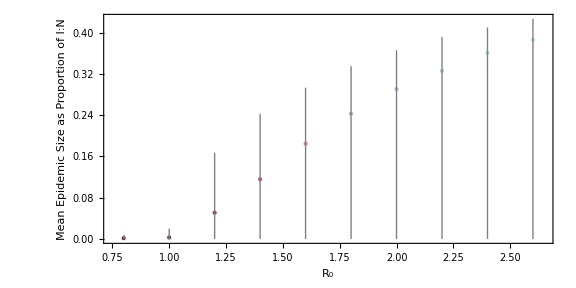

```mathematica
(* Helper for confidence intervals *)
CI95[data_] := Quantile[data, {0.025, 0.975}];

(* Epidemic size stats with 95% CI *)
MaxProportionInfectedStatsAssoc = Table[
  Module[{vals = simulationResults[r]["MaxProportionInfected"], ci},
    ci = CI95[vals];
    <|
      "R0" -> r,
      "MeanSize" -> N[Mean[vals]],
      "CI_Lower" -> N[ci[[1]]],
      "CI_Upper" -> N[ci[[2]]]
    |>
  ],
  {r, r0Values}
];
(* Colour palette *)
colorFunc = ColorData["CandyColors"];
meanSizes = MaxProportionInfectedStatsAssoc[[All, "MeanSize"]];
minSize = Min[meanSizes];
maxSize = Max[meanSizes];
normalizeSize[val_] := (val - minSize)/(maxSize - minSize);

(* Generate graphics elements *)
coloredSizePoints = Table[
  {
    colorFunc[normalizeSize[stat["MeanSize"]]],
    PointSize[Medium],
    Point[{stat["R0"], stat["MeanSize"]}],
    (* vertical error bar *)
    Gray,
    Line[{
      {stat["R0"], stat["CI_Lower"]},
      {stat["R0"], stat["CI_Upper"]}
    }]
  },
  {stat, MaxProportionInfectedStatsAssoc}
]
Graphics[
  coloredSizePoints /. PointSize[_] :> PointSize[Large],
  Frame -> True,
  FrameLabel -> {
    Style["R₀", 14],
    Style["Mean Epidemic Size as Proportion of I:N", 14]
  },
  PlotRange -> {{0.75, 2.65}, Automatic},
  AspectRatio -> 0.5,
  ImageSize -> Large,
  FrameTicks -> Automatic,
  GridLines -> None
]
```

#### What do the distributions of the values actually look like?

{1000,1000,2,1000,1000,1000,3,1000,2,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,4,1000,3,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,7,1000,1000,1000,1000,1000,1000,1000,1000,7,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,3,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,3,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,3,1000,1000,2,1000,1000,1000,3,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,5,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,3,1000,1000,1000,2,1000,1000,1000,1000,1000,4,1000,1000,1000,1000,3,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,2,1000,2,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,4,1000,1000,1000,7,1000,1000,1000,1000,1000,3,1000,7,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,6,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,3,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,3,1000,1000,1000,1000,1000,1000,1000,1000,5,1000,1000,1000,1000,1000,3,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,4,1000,1000,1000,1000,1000,1000,4,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,4,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,4,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,2,1000,1000,3,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,3,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,3,1000,1000,4,2,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,2,2,1000,3,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,2,3,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,7,2,1000,1000,2,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,3,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000}

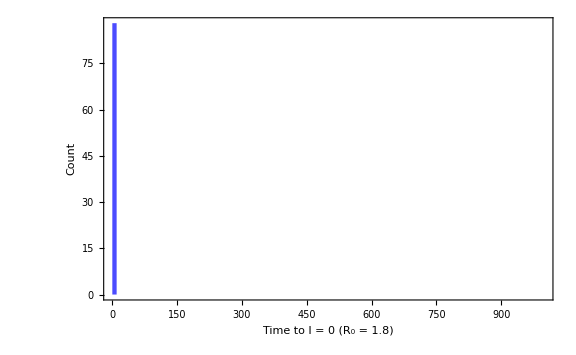

```mathematica
r = 1.8;
vals = simulationResults[r]["ExtinctionTimes"];
vals = Select[vals, # > 1 &]
Histogram[
  vals,
  {0, 1000, 10},  (* adjust bin size if needed *)
  "Count",
  Frame -> True,
  FrameLabel -> {
    "Time to I = 0 (R₀ = " <> ToString[r] <> ")",
    "Count"
  },
  ChartStyle -> Directive[Opacity[0.7], Blue],
  ImageSize -> Large
]
```